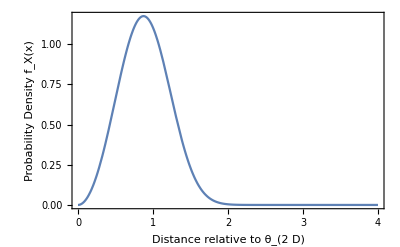

```mathematica
fX[x_]:=3*x^2*Exp[-x^3]
fY[y_]:=(3 (9 ⅇ^(-y^3) y^2+2 y^2 Gamma[0,y^3]+(3 (-4  y Gamma[4/3,y^3]+Gamma[5/3,y^3]))/(1)^(2/3)))/2

Plot[fX[x],{x,0,4}, PlotStyle-> Line,Frame-> True, FrameLabel->{"Distance relative  to θ_(2  D)", "Probability Density  f_X(x)"}, RotateLabel-> True]
```

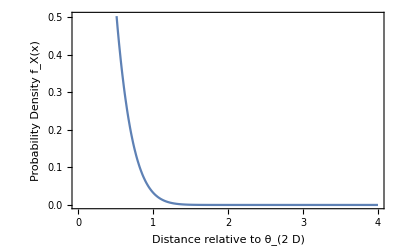

```mathematica
Plot[fY[x],{x,0,4}, PlotStyle-> Line,Frame-> True, FrameLabel->{"Distance relative  to θ_(2  D)", "Probability Density  f_X(x)"}, RotateLabel-> True]
```

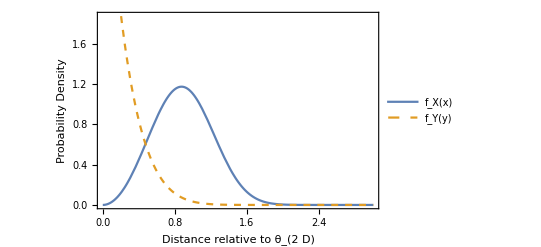

```mathematica
Plot[{fX[x], fY[x]},{x,0,3}, PlotStyle-> {Line, Dashed}, Frame-> True, FrameLabel-> {Style["Distance relative to θ_(2  D)", Bold, 12],Style["Probability Density", Bold, 12] }, RotateLabel->True, PlotLegends-> Placed[{"f_X(x)", "f_Y(y)"},Center]]
```